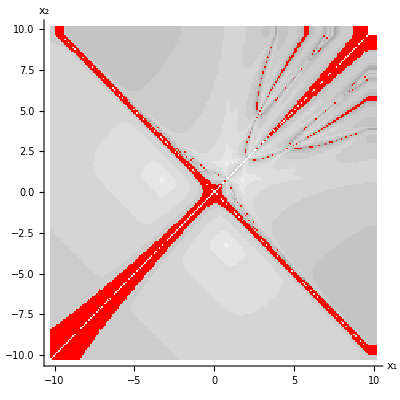

```mathematica
data=Import["/Users/ivandybko/Projects/Numerical_methods/Lab5/src/data/sys2_1.txt","Table"];


maxIterations=30; 
h1=h2=0.5; 

(*Создание цветовой палитры*)
colorFunction[n_]:=If[n==-1,Red,GrayLevel[1-n/maxIterations]];

(*Построение графика*)
graphics=Graphics[Table[Module[{x1=data[[i,1]],x2=data[[i,2]],iter=data[[i,3]]},{colorFunction[iter],Rectangle[{x1-h1/2,x2-h2/2},{x1+h1/2,x2+h2/2}]}],{i,Length[data]}]];

(*Отображение графика*)
gr=Show[graphics,Axes->True,AxesLabel->{"x_1","x_2"},PlotStyle->{FontFamily->"Times"}]
```

```mathematica
Export["/Users/ivandybko/Projects/Numerical_methods/Lab5/doc/sys2_0.1.eps",gr]
```

/Users/ivandybko/Projects/Numerical_methods/Lab5/doc/sys2_0.1.eps

```mathematica
"/Users/ivandybko/Projects/Numerical_methods/Lab5/doc/sys2_0.01.eps"
```

```mathematica
gr
```

$Aborted